## Solutions: Mathematica 6 Lab 1

Problem 1:

```mathematica
∫_0^π Cos[x Sin[θ]]ⅆθ
```

If[x∈Reals,π BesselJ[0,Abs[x]],Integrate[Cos[x Sin[θ]],{θ,0,π},Assumptions→Im[x]<0||Im[x]>0]]

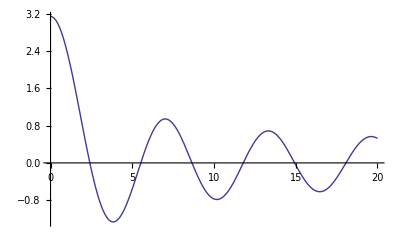

```mathematica
Plot[%,{x,0,20}]
```

```mathematica
Plot[Evaluate[∫_0^π Cos[x Sin[θ]]ⅆθ],{x,0,20}]
```

-Graphics-

```mathematica
?Evaluate
```

Evaluate[expr] causes expr to be evaluated even if it appears as the argument of a function whose attributes specify that it should be held unevaluated.

Problem 2:

```mathematica
Hyperlink["FibonacciBiography","http://en.wikipedia.org/wiki/Fibonacci"]
```

```mathematica
Fibonacci[51]/Fibonacci[50]//N
```

1.61803

```mathematica
Fibonacci[101]/Fibonacci[100]//N
```

1.61803

```mathematica
Fibonacci[100]/Fibonacci[101]//N
```

0.618034

```mathematica
Solve[x==1+1/x,x]
```

{{x→1/2 (1-√5)},{x→1/2 (1+√5)}}

```mathematica
1/2 (1+√5)//N
```

1.61803

```mathematica
GoldenRatio//N
```

1.61803

```mathematica
b=1/2 (1+√5)
```

1/2 (1+√5)

```mathematica
Log[Fibonacci[50]]-50Log[b]//N
Log[Fibonacci[100]]-100Log[b]//N
```

-0.804719

-0.804719

```mathematica
Log[1/√5]//N
```

-0.804719

```mathematica
a=1/√5
```

1/(√5)

```mathematica
N[Fibonacci[50]/(a b^50),40]
N[Fibonacci[100]/(a b^100),40]
```

0.9999999999999999999987374866619361570578

1.

```mathematica
Clear[k,x]
```

```mathematica
∑_(k=0)^∞ 1/(k!)Fibonacci[k] x^k
```

(ⅇ^(-(2 x)/(1+√5)) (-1+ⅇ^(((5+√5) x)/(1+√5))))/(√5)

```mathematica
Series[%,{x,0,6}]
```

((5+√5) x)/(√5 (1+√5))+((5+√5) x^2)/(2 √5 (1+√5))+(8 (5+2 √5) x^3)/(3 √5 (1+√5)^3)+((5+2 √5) x^4)/(√5 (1+√5)^3)+(2 (25+11 √5) x^5)/(3 √5 (1+√5)^5)+(8 (25+11 √5) x^6)/(45 √5 (1+√5)^5)+O[x]^7

```mathematica
Simplify[%]
```

x+x^2/2+x^3/3+x^4/8+x^5/24+x^6/90+O[x]^7

```mathematica
logfib=Table[Log[Fibonacci[k]],{k,1,100}]//N
```

{0.,0.,0.693147,1.09861,1.60944,2.07944,2.56495,3.04452,3.52636,4.00733,4.48864,4.96981,5.45104,5.93225,6.41346,6.89467,7.37588,7.85709,8.33831,8.81952,9.30073,9.78194,10.2632,10.7444,11.2256,11.7068,12.188,12.6692,13.1504,13.6316,14.1128,14.5941,15.0753,15.5565,16.0377,16.5189,17.0001,17.4813,17.9625,18.4438,18.925,19.4062,19.8874,20.3686,20.8498,21.331,21.8122,22.2934,22.7747,23.2559,23.7371,24.2183,24.6995,25.1807,25.6619,26.1431,26.6244,27.1056,27.5868,28.068,28.5492,29.0304,29.5116,29.9928,30.474,30.9553,31.4365,31.9177,32.3989,32.8801,33.3613,33.8425,34.3237,34.805,35.2862,35.7674,36.2486,36.7298,37.211,37.6922,38.1734,38.6547,39.1359,39.6171,40.0983,40.5795,41.0607,41.5419,42.0231,42.5043,42.9856,43.4668,43.948,44.4292,44.9104,45.3916,45.8728,46.354,46.8353,47.3165}

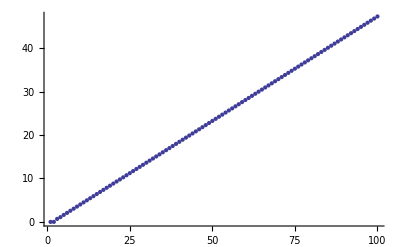

```mathematica
FibonacciPoints=ListPlot[logfib]
```

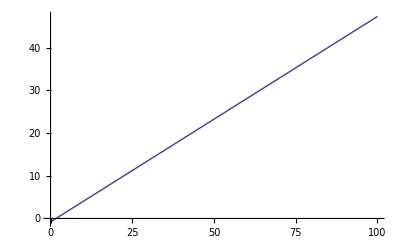

```mathematica
FibonacciLine=Plot[Log[a b^n] ,{n,0,100}]
```

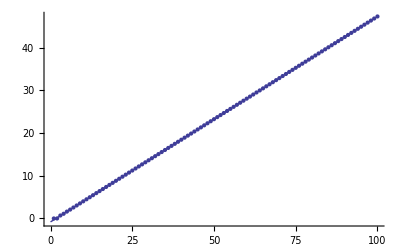

```mathematica
Show[FibonacciPoints, FibonacciLine]
```

Problem 3:

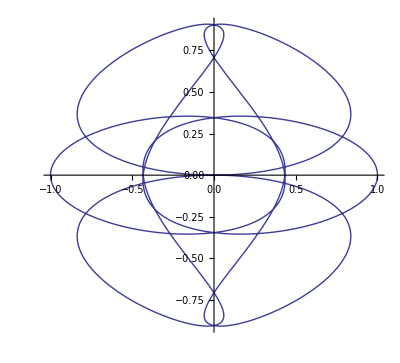

```mathematica
ParametricPlot[{Sin[5t]Cos[2t],Sin[3t]Sin[2t]},{t,0,2π}]
```

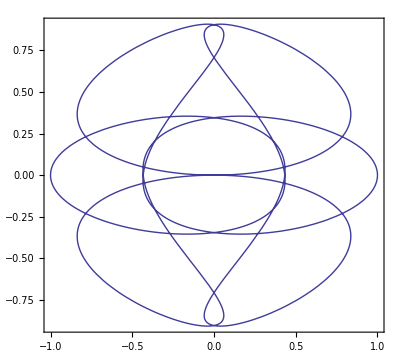

```mathematica
ParametricPlot[{Sin[5t]Cos[2t],Sin[3t]Sin[2t]},{t,0,2π},Axes->None,Frame->True]
```

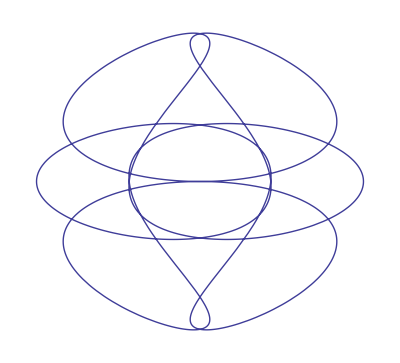

```mathematica
ParametricPlot[{Sin[5t]Cos[2t],Sin[3t]Sin[2t]},{t,0,2π},Axes->None,Frame->False,Ticks->False]
```

Problem 4:

```mathematica
f1[x_]:=Sin[x]
f2[x_]:=Sin[x]^2
f7[x_]:=Sin[x]^7
f8[x_]:=Sin[x]^8
```

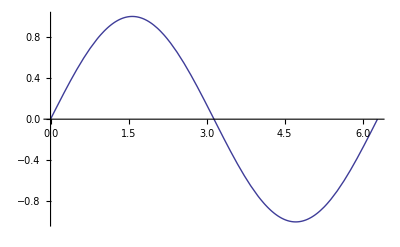

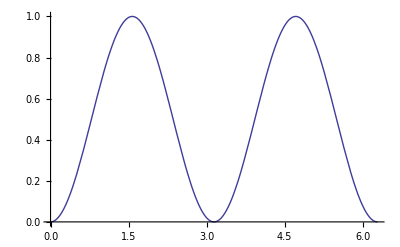

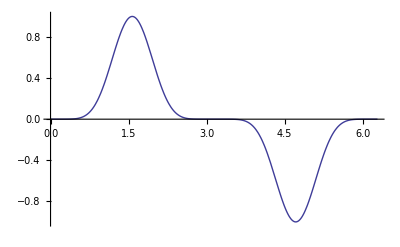

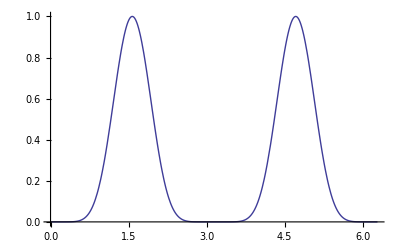

```mathematica
g1=Plot[f1[x],{x,0,2π},PlotRange->All]
g2=Plot[f2[x],{x,0,2π},PlotRange->All]
g7=Plot[f7[x],{x,0,2π},PlotRange->All]
g8=Plot[f8[x],{x,0,2π},PlotRange->All]
```

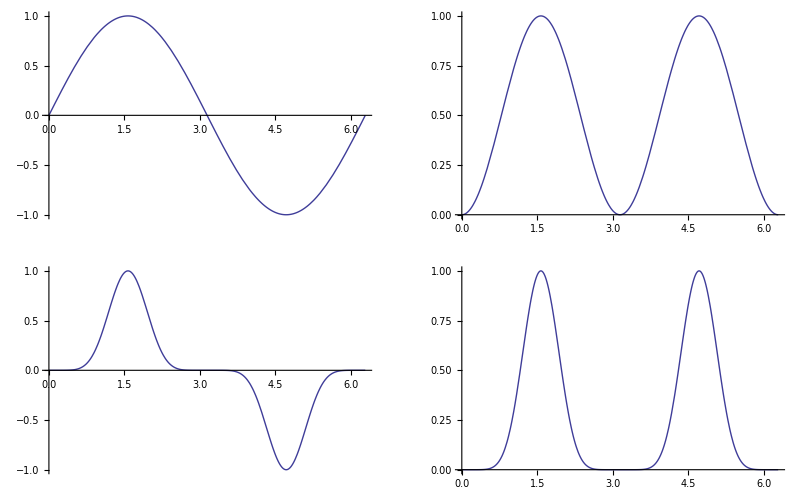

```mathematica
Show[GraphicsArray[{{g1,g2},{g7,g8}}]]
```

Problem 5:

```mathematica
f[x_]:=∑_(k=1)^30 1/(k+k^(1/3))Sin[2π k x]
```

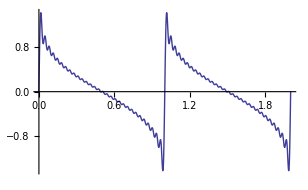
{5.15616,-Graphics-}

```mathematica
Plot[f[x],{x,0,2}]//Timing
```

Problem 6:

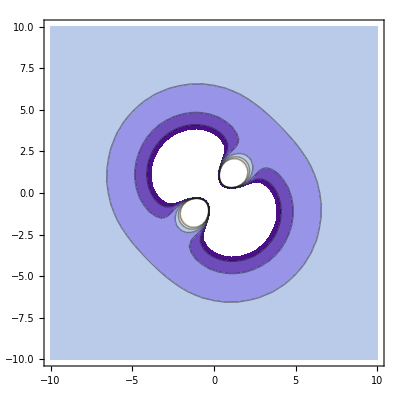

```mathematica
ContourPlot[1/((x-1)^2+(y-1)^2)-3/((x-1)^2+(y+1)^2)+1/((x+1)^2+(y+1)^2)-3/((x+1)^2+(y-1)^2), {x,-10,10},{y,-10,10}]
```

```mathematica
ContourPlot[1/((x-1)^2+(y-1)^2)-3/((x-1)^2+(y+1)^2)+1/((x+1)^2+(y+1)^2)-3/((x+1)^2+(y-1)^2), {x,-10,10},{y,-10,10},PlotPoints->100]
```

-Graphics-

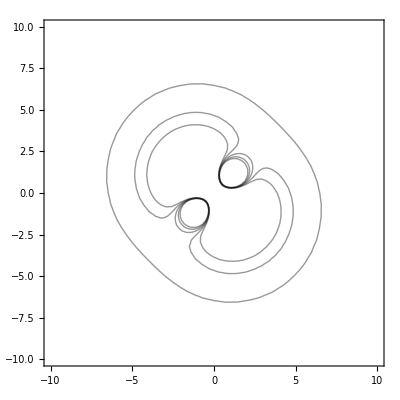

```mathematica
ContourPlot[1/((x-1)^2+(y-1)^2)-3/((x-1)^2+(y+1)^2)+1/((x+1)^2+(y+1)^2)-3/((x+1)^2+(y-1)^2), {x,-10,10},{y,-10,10},ContourShading->False]
```

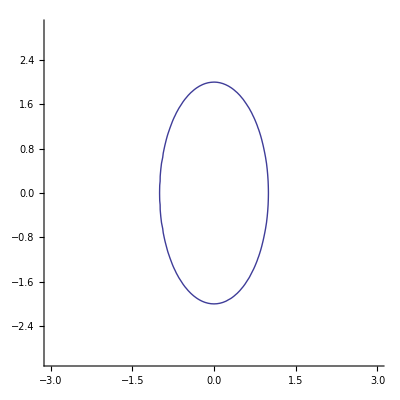

```mathematica
ContourPlot[x^2+y^2/4==1,{x,-3,3},{y,-3,3}, Frame->False,Axes->True]
```